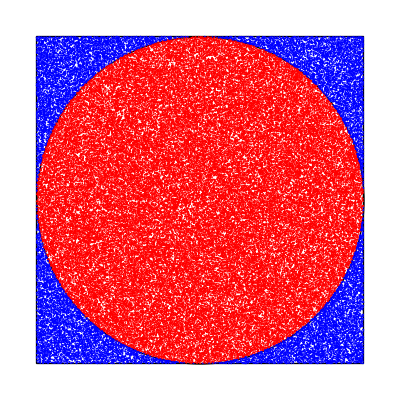

```mathematica
Get["C:\\Users\\Luka\\Documents\\ŠOLA\\FAKS\\Pouk\\3 Letnik\\Napredna računalniška orodja\\Matematica vaje\\Domača naloga\\mccpi.m"]

n=100000; (*Število točk*)
priblizekPi=piMonteCarlo[n];

tockeZnotraj=Select[RandomReal[{-1,1},{n,2}],Norm[#]<=1&];
tockeZunaj=Select[RandomReal[{-1,1},{n,2}],Norm[#]>1&];

krog=Graphics[{Circle[{0,0},1]}];
kvadrat=Graphics[{Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]}];
znotraj=ListPlot[tockeZnotraj,PlotStyle->Red];
zunaj=ListPlot[tockeZunaj,PlotStyle->Blue];

Show[{kvadrat,krog,znotraj,zunaj},AspectRatio->1,PlotRange->{{-1,1},{-1,1}}]
```